# Kompleksna števila

## Predstavitev:

Množica kompleksnih števil predstavlja razširitev realnih števil, v kateri se lahko koreni tudi negativna števila. Kompleksna števila vsebujejo imaginarno enoto ⅈ (ponekod tudi ⅉ), kjer velja ⅈ^2= -1. Kompleksna števila so oblike z = x + ⅈy, kjer je  x   realni del kompleksnega števila, y pa njegov imaginarni del.
Npr. prikaz kompleksnega števila 3+2ⅈ

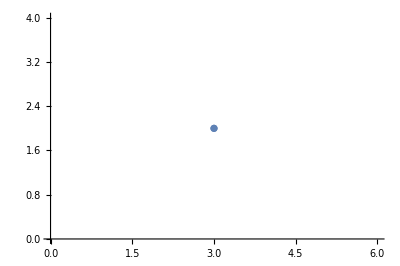

```mathematica
ComplexListPlot[{3 + 2I}]
```

Lahko se jih predstavi tudi kot: z = x + ⅈy=r(Cos[ϕ]+Sin[ϕ]) , kjer je r=|z| in ϕ = Arg(z). 
Dotaknili se bomo tudi kompleksne analize, natančneje holomorfne funkcije. To so funkcije, ki iz odprte podmnožice kompleksne ravnine slika v kompleksno ravnino in so odvedljive v kompleksnem v vsaki točki.
Pogledali si bomo tudi nalogo, pri kateri bomo z metodo ostankov izračunali integral po pozitivno orientirani krivulji.

## Naloge:

1. NALOGA:
Nariši množico kompleksnih števil, ki zadoščajo enačbi |z+1|= |2z-1|

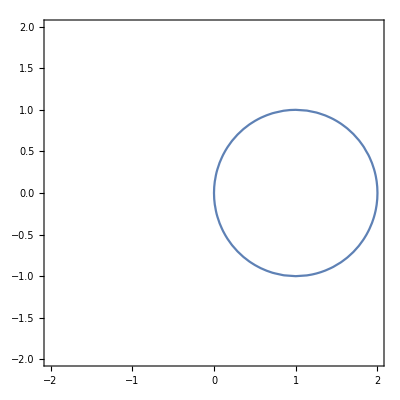

```mathematica
ComplexContourPlot[Abs[z+1]==Abs[2z-1],{z,-2-2 I,2+2 I}]
```

2. NALOGA:
Skiciraj podmnožico kompleksnih števil {π/4<arg(z)⩽π, 1<|z|⩽2} .
Pomisli kako bi izgledalo, če ne bi imeli pogoja za |z|.

Neenakost 1<|z|⩽2 določa kolobar z notranjim polmerom r = 1 in zunanjim R=2. Neenakost π/4<arg(z)⩽π pa izreže krožni izsek.

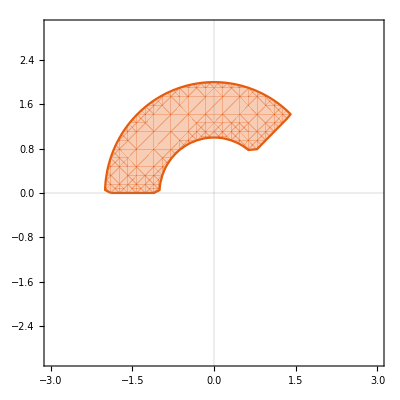

```mathematica
ComplexRegionPlot[1<Abs[z]≤2  && π/4<Arg[z]≤π, {z,-3 - 3I, 3 +3I}, PlotTheme-> "Scientific"]
```

Če ne bi imeli podanega pogoja za |z|, bi izgledalo takole:

```mathematica
Manipulate[ComplexRegionPlot[0<Abs[z]≤n && π/4<Arg[z]≤π, {z,-5 - I, 5 +10I}],{n, 0, 5}]
```

3. NALOGA:
Katera kompleksna števila zadoščajo pogojem: Re(z^2-2)<n in Im(z^2)<n, za n=1. Prikaži grafično.
Katera števila bi zadoščala za splošen |n|⩽2

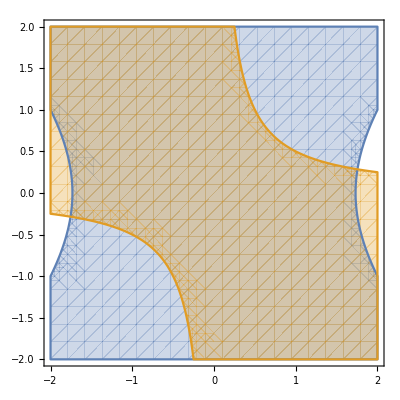

```mathematica
ComplexRegionPlot[{Re[z^2 - 2]< 1, Im[z^2] < 1},{z,2}]
```

```mathematica
Manipulate[ComplexRegionPlot[{Re[z^2- 2]< n, Im[z^2] < n},{z,2}],{n, -2, 2}]
```

4. NALOGA:
Z metodo ostankov (residumov) izračunajte integral od 1/(z^4 + 1) po pozitivno orientirani krivulji |z-1|=1 .   (∫_(|z-1|=1) 1/(z^4 + 1)ⅆz)

Podintegralska funkcija f(z)=1/(z^4 + 1) ima štiri enostavne pole, rešitve enačbe z^4=-1 . To so: z_k = ⅇ^(ⅈ(2k+1)π/4) = Cos[(2k+1)π/4]+ⅈSin[(2k+1)π/4] , k = 0,1,2,3.

```mathematica
nicle = ComplexListPlot[Callout[#, #] & /@ Table[E^(π I (2 k + 1)/4), {k, 0, 3}]]
```

-Graphics-

Vidimo, da znotraj krožnice |z-1|=1 ležita z_0 = ⅇ^(ⅈ π/4)  in z_3 = ⅇ^(-ⅈ π/4).
Slika:      -Graphics-
Ostanka funkcije f(z) v teh dveh polih sta:

Res(f(z),z_0)=1/(4 z_0^3)=ⅇ^(-3 ⅈ π/4)/4
 Res(f(z),z_3)=1/(4 z_3^3)=ⅇ^(3 ⅈ π/4)/4

Torej je ∫_(|z-1|=1) 1/(z^4 + 1)ⅆz  = 2πⅈ(Res(f(z),z_0) + Res(f(z),z_3)) =πⅈ/2( ⅇ^(3ⅈ π/4) + ⅇ^(-3ⅈ π/4)) 
Ker je (ⅇ^(3ⅈ π/4) + ⅇ^(-3ⅈ π/4))/2=Cos[(3π)/4]=-(√2)/2  , je končen rezultat enak ∫_(|z-1|=1) 1/(z^4 + 1)ⅆz  = (-√2π ⅈ)/2 .

5.NALOGA:
Poišči sliko kolobarja 1<|z|<2 s preslikavo w=f(z)=z/(z-1)

Izrazimo inverzno funkcijo in dobimo  z=f^-1(w)=w/(w-1).
Ker imamo pogoj 1< |z|<2, vemo, da sta enačbi notranja in zunanja mejna krožnica kolobarja:z z̄= 1,z z̄= 4 
Ko vstavimo  z=w/(w-1) v zgornji enačbi, dobimo w/(w-1)(w̄)/(w̄-1)=1, w/(w-1)(w̄)/(w̄-1)=4, iz katerih dobimo enačbi: w +w̄ -1=0, 3w w̄ -4w -4 w̄  +4 =0. Če rečemo, da je w=u + ⅈv , dobimo: 2u=1,3 u^2+3v^2 - 8u + 4 =0

Poglejmo si, kako izgleda: 1< |z|<2

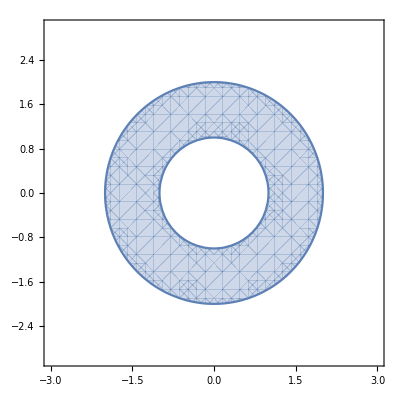

```mathematica
ComplexRegionPlot[1<Abs[z]≤2 ,{z,-3 - 3I, 3 +3I}]
```

in sedaj preslikano s preslikavo w=f(z)=z/(z-1)

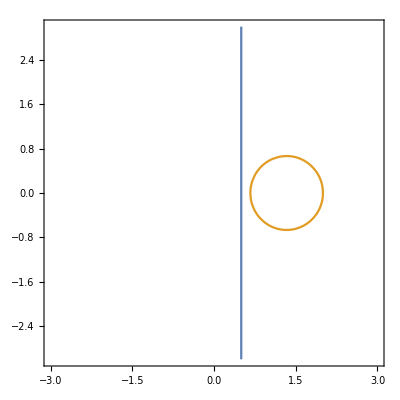

```mathematica
ContourPlot[{2 x==1, 3 x^2 + 3 y^2 - 8 x + 4==0 },{x, -3, 3},{y,-3, 3}]
```

Točka z=3/2 je znotraj kolobarja in se preslika v w=f(3/2) = 3  znotraj preslikanega območja. Prva krivulja je premica u=1/2, druga pa krožnica (u - 4/3)^2+v^2 =4/9